# Confluence in Multiway Cellular Automata

## Ben Jacobsohn

## Project Description

Multiway cellular automata are a modification of cellular automata where different rules are applied at every step. The goal of this project is to study this type of system and find how different paths in the multiway graph will branch and merge depending on the rule applied at each step. Another way the system could be constructed is to apply different rules depending on the spatial position in the row. I hope to use these results to construct automata that will perform useful computations.

## Multiway Cellular Automata Implementation

```mathematica
(* From NKS Chapter 2 Notes *)
ElementaryRule[num_Integer]:=IntegerDigits[num,2,8]
CAStep[rule_,a_]:=rule[[8-ListConvolve[{1,2,4},a,2]]]
```

```mathematica
(* Multiway Functions *)
Clear[multiCAStep];multiCAStep[elemRules_List,state_List]:=state->CAStep[ElementaryRule@#,state]&/@elemRules
```

```mathematica
rules={30,50}
```

{30,50}

```mathematica
initialState=CenterArray[1,10]
```

{0,0,0,0,1,0,0,0,0,0}

```mathematica
CAStep[rules[[1]],initialState]
```

{0,0,0,1,1,1,0,0,0,0}

```mathematica
l1=multiCAStep[rules,initialState]
```

{{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,0,1,0,0,0,0}}

```mathematica
l2=Flatten[multiCAStep[rules,#]&/@Values[l1]]
```

{{0,0,0,1,1,1,0,0,0,0}→{0,0,1,1,0,0,1,0,0,0},{0,0,0,1,1,1,0,0,0,0}→{0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0}→{0,0,1,1,0,1,1,0,0,0},{0,0,0,1,0,1,0,0,0,0}→{0,0,1,0,1,0,1,0,0,0}}

```mathematica
l3=Flatten[multiCAStep[rules,#]&/@Values[l2]]
```

{{0,0,1,1,0,0,1,0,0,0}→{0,1,1,0,1,1,1,1,0,0},{0,0,1,1,0,0,1,0,0,0}→{0,1,0,0,1,1,0,1,0,0},{0,0,1,0,0,0,1,0,0,0}→{0,1,1,1,0,1,1,1,0,0},{0,0,1,0,0,0,1,0,0,0}→{0,1,0,1,0,1,0,1,0,0},{0,0,1,1,0,1,1,0,0,0}→{0,1,1,0,0,1,0,1,0,0},{0,0,1,1,0,1,1,0,0,0}→{0,1,0,0,1,0,0,1,0,0},{0,0,1,0,1,0,1,0,0,0}→{0,1,1,0,1,0,1,1,0,0},{0,0,1,0,1,0,1,0,0,0}→{0,1,0,1,0,1,0,1,0,0}}

```mathematica
layers=Flatten[{l1,l2,l3}];
```

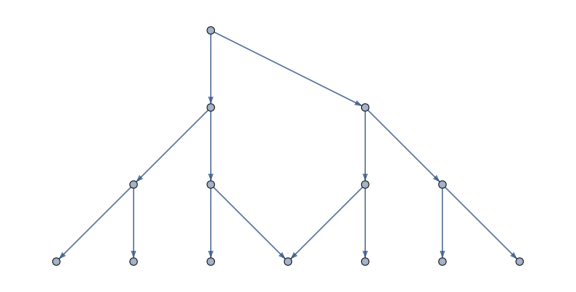

```mathematica
Graph[layers,
VertexLabels->(#->Placed[ArrayPlot[{#},ImageSize->Tiny],Tooltip]&)/@Values@layers,
ImageSize->Large]
```

## v2

```mathematica
Clear[multiStep];multiStep[rules_,state_]:=(state->CellularAutomaton[#,state])&/@rules
```

```mathematica
Flatten[multiStep[rules,#]&/@Values[init],1]
```

{{0,0,0,1,1,1,0,0,0,0},{0,0,0,1,0,1,0,0,0,0}}

```mathematica
Flatten[multiStep[rules,#]&/@%,1]
```

{{0,0,1,1,0,0,1,0,0,0},{0,0,1,0,0,0,1,0,0,0},{0,0,1,1,0,1,1,0,0,0},{0,0,1,0,1,0,1,0,0,0}}

```mathematica
newStates=Flatten[multiStep[rules,#]&/@Values@init,1]
```

{{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,0,1,0,0,0,0}}

```mathematica
Flatten[multiStep[rules,#]&/@Values@newStates,1]
```

{{0,0,0,1,1,1,0,0,0,0}→{0,0,1,1,0,0,1,0,0,0},{0,0,0,1,1,1,0,0,0,0}→{0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0}→{0,0,1,1,0,1,1,0,0,0},{0,0,0,1,0,1,0,0,0,0}→{0,0,1,0,1,0,1,0,0,0}}

```mathematica
init
```

{{0,0,0,0,0,0,0,0,0,0}→{0,0,0,0,1,0,0,0,0,0}}

```mathematica
Values@init
```

{{0,0,0,0,1,0,0,0,0,0}}

```mathematica
NestList[Flatten[multiStep[rules,#]&/@Values@#&,1],init,3]
```

CellularAutomaton::initn: The initial condition specification {{{0,0,0,1,1,0,0,1,0,0,«2»},{0,0,0,1,1,0,1,1,0,0}},{{0,0,0,1,0,0,0,1,0,0,«2»},{0,0,0,1,0,1,0,1,0,0}}} should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

{{{0,0,0,0,0,0,0,0,0,0}→{0,0,0,0,1,0,0,0,0,0}},{{{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,0,1,0,0,0,0}}},{{{{0,0,0,1,1,1,0,0,0,0},{0,0,0,1,0,1,0,0,0,0}}→{{0,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0}},{{0,0,0,1,1,1,0,0,0,0},{0,0,0,1,0,1,0,0,0,0}}→{{0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0}}}},{{{{{0,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0}},{{0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0}}}→CellularAutomaton[30,{{{0,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0}},{{0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0}}}],{{{0,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0}},{{0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0}}}→CellularAutomaton[50,{{{0,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0}},{{0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0}}}]}}}